# Check Trapezoid function

```mathematica
Get["NeutronBeam/NeutronBeamDefinition.m"]
```

```mathematica
?TrapezNBeamNew
```

Global`TrapezNBeamNew

TrapezNBeamNew[xn_,{tw_,pl_,k1_,k2_,k3_}]:=Piecewise[{{0,xn<-tw/2},{k1 xn+(k1 tw)/2,-tw/2≤xn<-(2 k2 pl-2 k3 pl+(k1+k3) tw)/(2 (k1-k3))},{k2 xn+(-2 (k1-k2) (k2-k3) pl+(k1 (k2-2 k3)+k2 k3) tw)/(2 (k1-k3)),-(2 k2 pl-2 k3 pl+(k1+k3) tw)/(2 (k1-k3))≤xn<-(2 (-k1+k2) pl+(k1+k3) tw)/(2 (k1-k3))},{k3 xn-(k3 tw)/2,-(2 (-k1+k2) pl+(k1+k3) tw)/(2 (k1-k3))≤xn≤tw/2},{0,xn>tw/2}}]

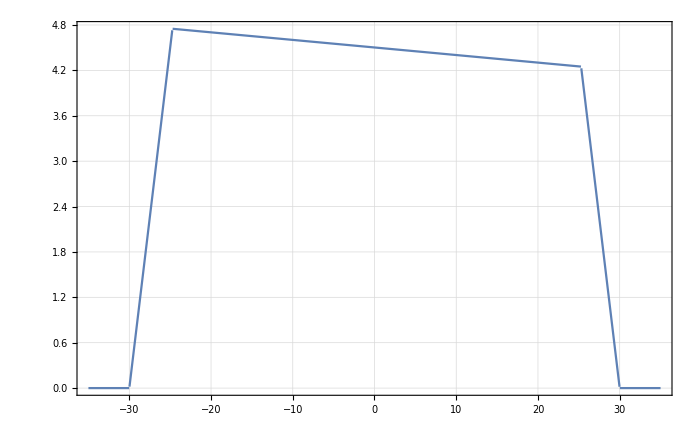

```mathematica
Plot[TrapezNBeamNew[xn,{60,50,0.9,-0.01,-0.9}],{xn,-35,35}]
```

### 2D

```mathematica
Plot3D[TrapezNBeamNew[xn,{60,50,0.9,-0.01,-0.9}]*TrapezNBeamNew[yn,{100,90,0.9,-0.01,-0.9}],{xn,-35,35},{yn,-55,55}]
```

-Graphics3D-

### is the norm of the 2D trapezoid the same as the 2 1D norms?

```mathematica
NIntegrate[TrapezNBeamNew[xn,{60,50,0.9,-0.01,-0.9}]*TrapezNBeamNew[yn,{100,90,0.9,-0.01,-0.9}],{xn,-35,35},{yn,-55,55}]
```

105892.

```mathematica
NIntegrate[TrapezNBeamNew[xn,{60,50,0.9,-0.01,-0.9}],{xn,-35,35}]
```

247.569

```mathematica
NIntegrate[TrapezNBeamNew[yn,{100,90,0.9,-0.01,-0.9}],{yn,-55,55}]
```

427.725

```mathematica
247.5694444444444*427.7250000000009
```

105892.

### yes

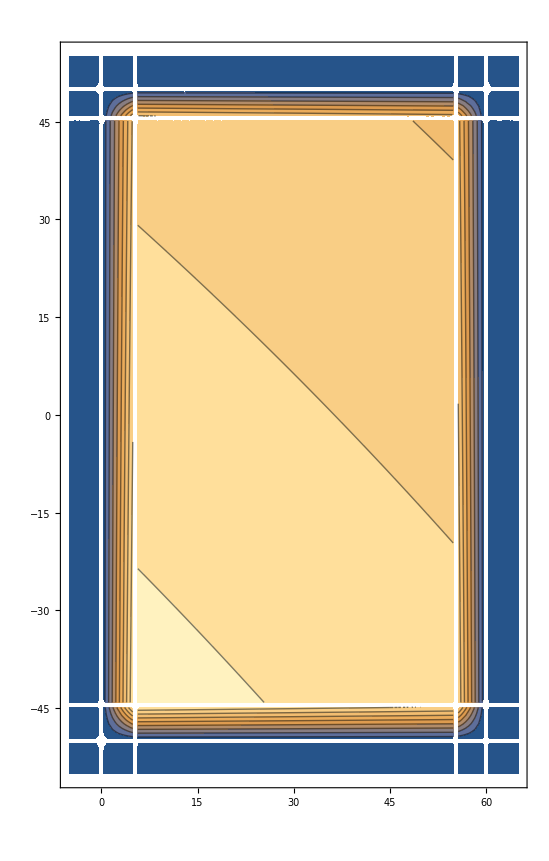

```mathematica
ContourPlot[TrapezNBeamNew[xn-30,{60,50,0.9,-0.01,-0.9}]*TrapezNBeamNew[yn,{100,90,0.9,-0.01,-0.9}],{xn,-5,65},{yn,-55,55},AspectRatio->Automatic]
```

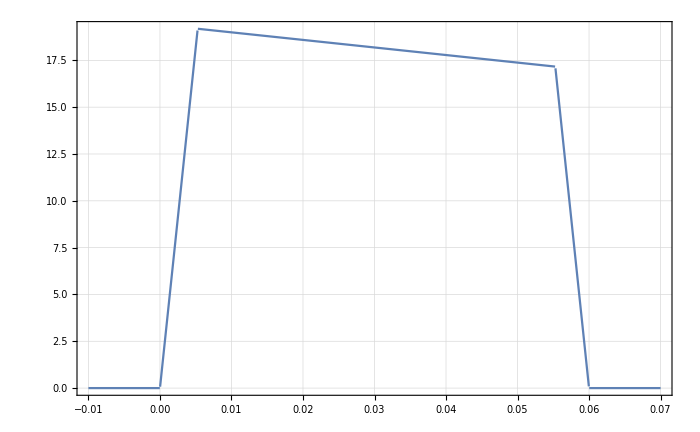

```mathematica
Plot[TrapezNBeamNewNormed[xn-0.030,{0.060,0.050,0.9,-0.01,-0.9}],{xn,-0.010,0.070}]
```

# Integrand v1 (has the x0 and y0 replacement rules in the 2D trapecoidal functions - as well as xOff/yOff)

```mathematica
Integrand2DArithBGradDetSpreadNBeam[b_?NumericQ,{xD_?NumericQ,yD_?NumericQ,phi_?NumericQ,p_?NumericQ,th0_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ},{xA_?NumericQ,yA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ,rA_?NumericQ},{R0_?NumericQ,G1_?NumericQ,G2_?NumericQ},{phiDV_,twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_}]:=

wmomNormedWb[λ0,κ0,b,p]*Sin[th0]*

TrapezNBeamNewNormed[(xD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Sin[phi])*Sqrt[rD/rRxB]+D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],R0,G1,G2]+rG[p,th0,rA*BRxB/rRxB]*Cos[phiDV]-xOff,{twx,plx,k1x,k2x,k3x}]*

TrapezNBeamNewNormed[(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB]+rG[p,th0,rA*BRxB/rRxB]*Sin[phiDV]-yOff,{twy,ply,k1y,k2y,k3y}]*

ArithApert[xA,yA,xOff,yOff,
(xD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Sin[phi])*Sqrt[rD/rRxB]+D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],R0,G1,G2],(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],
rG[p,theta2[th0,rA],rA*BRxB/rRxB]
]
```

```mathematica
Plot3D[Integrand2DArithBGradDetSpreadNBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}],{phiDV,0,2*Pi},{phi,0,2*Pi},AxesLabel->{"phiDV","phi","Integrand"}]
```

-Graphics3D-

### we first saw no phiDV dependence for varying xD. To investigate, we check, what parameter space xn goes into the nbeam function.

```mathematica
Plot3D[((xD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Sin[phi])*Sqrt[rD/rRxB]+D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],R,G1,G2]+rG[p,th0,rA*BRxB/rRxB]*Cos[phiDV]-xOff)/.
{xD->0.035,p->500000,th0->Pi/4,BRxB->0.2,rRxB->1,rD->1.,rA->1,alpha->Pi,yD->0.,R->1,G1->1,G2->1,xOff->0.04},{phiDV,0,2*Pi},{phi,0,2*Pi},PlotRange->{0,0.03}]
```

-Graphics3D-

### only for xD > 0.03, we hit the nbeam range limit of +0,03 m. Maybe, the integrand is there already completely zero for another reason (apert func?)

### above, we now did k2 unequal zero, then we should easier see an effect of nbeam through phiDV-> and we do for very strong k2’s

### now we just switch off neutron beam in integrand to directly compare

```mathematica
Integrand2DArithBGradDetSpreadNoBeam[b_?NumericQ,{xD_?NumericQ,yD_?NumericQ,phi_?NumericQ,p_?NumericQ,th0_?NumericQ,alpha_?NumericQ,BRxB_?NumericQ,rRxB_?NumericQ,rD_?NumericQ},{xA_?NumericQ,yA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ,rA_?NumericQ},{R0_?NumericQ,G1_?NumericQ,G2_?NumericQ},{phiDV_,twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_}]:=

wmomNormedWb[λ0,κ0,b,p]*Sin[th0]*

ArithApert[xA,yA,xOff,yOff,
(xD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Sin[phi])*Sqrt[rD/rRxB]+D1stBPolyGrad[p,alpha,th0,BRxB,rRxB,(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],R0,G1,G2],(yD+rG[p,theta2[th0,rD],rD*BRxB/rRxB]*Cos[phi])*Sqrt[rD/rRxB],
rG[p,theta2[th0,rA],rA*BRxB/rRxB]
]
```

```mathematica
Plot3D[
{
Integrand2DArithBGradDetSpreadNoBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}],
Integrand2DArithBGradDetSpreadNBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}]
},{phiDV,0,2*Pi},{phi,0,2*Pi},AxesLabel->{"phiDV","phi","Integrand"},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[
{
100*Integrand2DArithBGradDetSpreadNoBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}],
Integrand2DArithBGradDetSpreadNBeam[0,{0.0,0,phi,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{phiDV,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}]
},{phiDV,0,2*Pi},{phi,0,2*Pi},AxesLabel->{"phiDV","phi","Integrand"}]
```

-Graphics3D-

### its just that the scale of the 2 integrands is completely different..

```mathematica
Integrand2DArithBGradDetSpreadNoBeam[0,{0.0,0,3.Pi/2,1100000,Pi/4,Pi,0.2,1,1},{0.01,0.035,0.04,0.,1},{1,1,1},{0,0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9}]
```

3.98526×10^-8

### one trapez function factors the integrand by a factor of 10, so a factor of at least 100 seems reasonable

# Option 3: Apert(x_traj_A,y_traj_A) with boole

```mathematica
Get["NeutronBeam/NBeamIntegrand+Integration.m"]
```

Part::partw: Part {1,4} of {} does not exist.

## 3.1: With integration of xDV, yDV, ϕDV

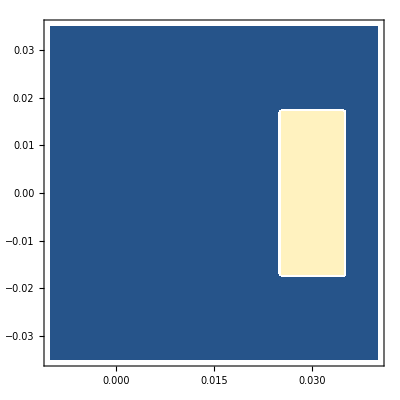

```mathematica
ContourPlot[ApertBoole[xtraj,ytraj,{0.01,0.035,0.03,0.}],{xtraj,-0.01,0.04},{ytraj,-0.035,0.035}]
```

### why does xA not depend on phiDV???? check

### oh, drift was defined in positive direction, thats why we have to choose positive xD currently

### Integrand plots

```mathematica
Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDet,700000,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],{phiDV,0,2*Pi},{phiDet,0,2*Pi},PlotPoints->50]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDet,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],{phiDV,0,2*Pi},{phiDet,0,2*Pi},PlotPoints->50],{{p,700000},0,pmax,100000}]
```

```mathematica
Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDV,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],{phiDV,0,2*Pi},{p,0,pmax},PlotPoints->50]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDet,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],{phiDV,0,2*Pi},{p,0,pmax},PlotPoints->10],{phiDet,0,2*Pi,2*Pi/4}]
```

### took 38s

### well here we treat all the phis as the same, but actually they are probably not, at least phiDet could be disconnected -> its own integration variable!

now you can again get limits for p by investigating aperture limits DOESNT WORK FOR NOW

### purely symbolic solving not possible (see this subsection)

```mathematica
testsolve=Solve[0.005==xA[phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],p]
```

{{p→-((0.333333 BRxB rD 1 Csc[th0] (-4.4819×10^16 G1 R √(1/rA) √rA √(rD/rRxB) rRxB Cos[phiA]+8.96379×10^16 G2 rD yD Cos[phiA]+4.4819×10^16 G1 R rA Cos[phiDet]-8.96379×10^16 G2 √(1/rA) rA^1 √(rD/rRxB) yD Cos[phiDet]+2.24095×10^14 G2 rA Sin[phiDet]-4.4819×10^16 G2 √(1/rA) rA^(3/2) √(rD/rRxB) xD Sin[phiDet]))/(G2 rRxB (-1.49896×10^8 rD Cos[phiA]+1.49896×10^8 √(1/rA) rA^(3/2) √(rD/rRxB) Cos[phiDet])))+1/(G2 3 1^1)-((0.132283+0.229122 ⅈ) Csc[phiDet]^2 Csc[th0]^3 (1)^(1/3))/(G2 rRxB^3 (-1.49896×10^8 rD Cos[phiA]+1.49896×10^8 3 Cos[phiDet]) √(1.-1. rRxB Sin[th0]^2))},{p→1},{p→1}}
 |  |  |  |

```mathematica
testsolve/.{phiA->0,yD->0,xD->0.03,th0->Pi/4,alpha->Pi,BRxB->0.2,rRxB->1,rA->1,rD->1,phiDet->0,R->1,G1->1,G2->1}
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √2 ComplexInfinity ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^(1/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) 2 √2 ComplexInfinity ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) 2 √2 ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{p→Indeterminate},{p→Indeterminate},{p→Indeterminate}}

```mathematica
Solve[0.005==xA[phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]/.{phiA->0,yD->0,xD->0.03,th0->Pi/4,alpha->Pi,BRxB->0.2,rRxB->1,rA->1,rD->1,phiDet->0,R->1,G1->1,G2->1},p]
```

{{p→449847.}}

```mathematica
Solve[-0.005==xA[phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]/.{phiA->0,yD->0,xD->0.03,th0->Pi/4,alpha->Pi,BRxB->0.2,rRxB->1,rA->1,rD->1,phiDet->0,R->1,G1->1,G2->1},p]
```

{{p→629785.}}

### so we have to put in numeric values to solve. it depends on phi, so we might have to change integration order, phi after p

```mathematica
ClearAll[pminApert]
```

```mathematica
Plot3D[xA[phiA,0.,0.03,800000,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1],{phiA,0,2Pi},{phiDet,0,2Pi}]
```

-Graphics3D-

```mathematica
pminApert[phiA_,yD_,xD_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_?NumericQ,R_,G1_,G2_,xOff_,xAA_]:=Solve[xOff+xAA/2==xA[phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],p][[1,1,2]]
```

```mathematica
pminApert[0.,0.,0.03,Pi/8,Pi,0.2,1,1,1,0.,1,1,1,0.,0.01]
```

475643.

```mathematica
pminApert[phiA,0.,0.03,Pi/8,Pi,0.2,1,1,1,0.,1,1,1,0.,0.01]
```

0.025/(5.89429×10^-8-6.38247×10^-9 Cos[phiA])

```mathematica
pminApert[0.,0.,0.03,Pi/8,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(1.30566×10^6 (36.9552 Sin[phiDet]-36.9552 Cos[phiDet] Sin[phiDet]+0.92388 Sin[phiDet]^2))/(-0.92388 Sin[phiDet]^2+0.92388 Cos[phiDet] Sin[phiDet]^2)+((1.01739×10^-21-1.76218×10^-21 ⅈ) (-6.53594×10^53 (36.9552 Sin[phiDet]-36.9552 Cos[phiDet] Sin[phiDet]+0.92388 Sin[phiDet]^2)^2+1.60848×10^44 (1.30375×10^14+1.80198×10^13 Cos[phiDet]-4.50495×10^11 Sin[phiDet]) (-0.92388 Sin[phiDet]^2+0.92388 Cos[phiDet] Sin[phiDet]^2)))/((-0.92388 Sin[phiDet]^2+0.92388 Cos[phiDet] Sin[phiDet]^2) (1.78984×10^87 Sin[phiDet]^3-3.39301×10^87 Cos[phiDet] Sin[phiDet]^3+1.41649×10^87 Cos[phiDet]^2 Sin[phiDet]^3+1.86675×10^86 Cos[phiDet]^3 Sin[phiDet]^3+5.94133×10^85 Sin[phiDet]^4-6.94138×10^85 Cos[phiDet] Sin[phiDet]^4+1.00004×10^85 Cos[phiDet]^2 Sin[phiDet]^4-5.00022×10^82 Sin[phiDet]^5+5.00022×10^82 Cos[phiDet] Sin[phiDet]^5+8.3337×10^80 Sin[phiDet]^6+√((1.78984×10^87 Sin[phiDet]^3-3.39301×10^87 Cos[phiDet] Sin[phiDet]^3+1.41649×10^87 Cos[phiDet]^2 Sin[phiDet]^3+1.86675×10^86 Cos[phiDet]^3 Sin[phiDet]^3+5.94133×10^85 Sin[phiDet]^4-6.94138×10^85 Cos[phiDet] Sin[phiDet]^4+1.00004×10^85 Cos[phiDet]^2 Sin[phiDet]^4-5.00022×10^82 Sin[phiDet]^5+5.00022×10^82 Cos[phiDet] Sin[phiDet]^5+8.3337×10^80 Sin[phiDet]^6)^2+4. (-6.53594×10^53 (36.9552 Sin[phiDet]-36.9552 Cos[phiDet] Sin[phiDet]+0.92388 Sin[phiDet]^2)^2+1.60848×10^44 (1.30375×10^14+1.80198×10^13 Cos[phiDet]-4.50495×10^11 Sin[phiDet]) (-0.92388 Sin[phiDet]^2+0.92388 Cos[phiDet] Sin[phiDet]^2))^3))^(1/3))-((6.40918×10^-22+1.1101×10^-21 ⅈ) (1.78984×10^87 Sin[phiDet]^3-3.39301×10^87 Cos[phiDet] Sin[phiDet]^3+1.41649×10^87 Cos[phiDet]^2 Sin[phiDet]^3+1.86675×10^86 Cos[phiDet]^3 Sin[phiDet]^3+5.94133×10^85 Sin[phiDet]^4-6.94138×10^85 Cos[phiDet] Sin[phiDet]^4+1.00004×10^85 Cos[phiDet]^2 Sin[phiDet]^4-5.00022×10^82 Sin[phiDet]^5+5.00022×10^82 Cos[phiDet] Sin[phiDet]^5+8.3337×10^80 Sin[phiDet]^6+√((1.78984×10^87 Sin[phiDet]^3-3.39301×10^87 Cos[phiDet] Sin[phiDet]^3+1.41649×10^87 Cos[phiDet]^2 Sin[phiDet]^3+1.86675×10^86 Cos[phiDet]^3 Sin[phiDet]^3+5.94133×10^85 Sin[phiDet]^4-6.94138×10^85 Cos[phiDet] Sin[phiDet]^4+1.00004×10^85 Cos[phiDet]^2 Sin[phiDet]^4-5.00022×10^82 Sin[phiDet]^5+5.00022×10^82 Cos[phiDet] Sin[phiDet]^5+8.3337×10^80 Sin[phiDet]^6)^2+4. (-6.53594×10^53 (36.9552 Sin[phiDet]-36.9552 Cos[phiDet] Sin[phiDet]+0.92388 Sin[phiDet]^2)^2+1.60848×10^44 (1.30375×10^14+1.80198×10^13 Cos[phiDet]-4.50495×10^11 Sin[phiDet]) (-0.92388 Sin[phiDet]^2+0.92388 Cos[phiDet] Sin[phiDet]^2))^3))^(1/3))/(-0.92388 Sin[phiDet]^2+0.92388 Cos[phiDet] Sin[phiDet]^2)

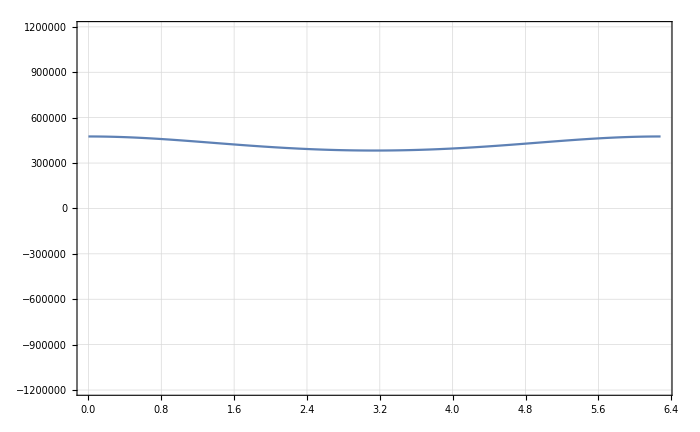

```mathematica
Plot[pminApert[phiA,0.,0.03,Pi/8,Pi,0.2,1,1,1,2Pi,1,1,1,0.,0.01],{phiA,0,2Pi},PlotRange->{-pmax,pmax}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

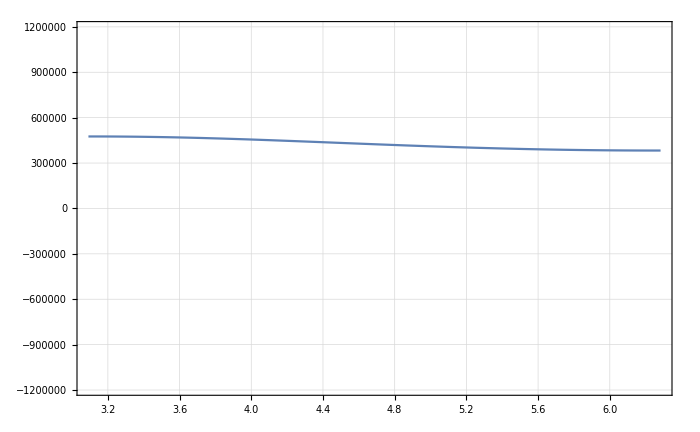

```mathematica
Plot[pminApert[Pi,0.,0.03,Pi/8,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],{phiDet,0,2Pi},PlotRange->{-pmax,pmax}]
```

```mathematica
Plot3D[pminApert[phiA,0.,0.03,Pi/8,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],{phiA,0,2Pi},{phiDet,0,2Pi},PlotRange->{-pmax,pmax}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[pminNBeam[phiA,0.,0.03,th0,Pi,0.2,1,1,1,phiA,1,1,1,0.,0.01],{th0,0,Pi/4},{phiA,0,2Pi}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

```mathematica
pmaxApert[phiA_,yD_,xD_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_,R_,G1_,G2_,xOff_,xAA_]:=Solve[xOff-xAA/2==xA[phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],p][[1,1,2]]
```

```mathematica
pmaxApert[0.,0.,0.03,Pi/8,Pi,0.2,1,1,1,0.,1,1,1,0.,0.01]
```

665900.

```mathematica
pmaxNBeam[phiA,0.,0.03,Pi/8,Pi,0.2,1,1,1,0.,1,1,1,0.,0.01]
```

pmaxNBeam[phiA,0.,0.03,π/8,π,0.2,1,1,1,0.,1,1,1,0.,0.01]

### stays easy with phiDV and phiA symbolical. phiDet creates mess!

### pmax and pmin are currently switched because D1st is in positive direction!

```mathematica
ClearAll[pminNBeamCases,pmaxNBeamCases]
```

```mathematica
pminNBeamCases[phiA_,yD_,xD_,th0_?NumericQ,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_?NumericQ,R_,G1_,G2_,xOff_,xAA_]:=Module[
{pminlocal=Re[pminNBeam[phiA,yD,xD,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,xOff,xAA]]},
Piecewise[
{
{0,pminlocal<0},
{pmax,pminlocal>pmax}
},
pminlocal
]
]
```

```mathematica
pmaxNBeamCases[phiA_,yD_,xD_,th0_?NumericQ,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_?NumericQ,R_,G1_,G2_,xOff_,xAA_]:=Module[
{pmaxlocal=Re[pmaxNBeam[phiA,yD,xD,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,xOff,xAA]]},
Piecewise[
{
{0,pmaxlocal<0},
{pmax,pmaxlocal>pmax}
},
pmaxlocal
]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

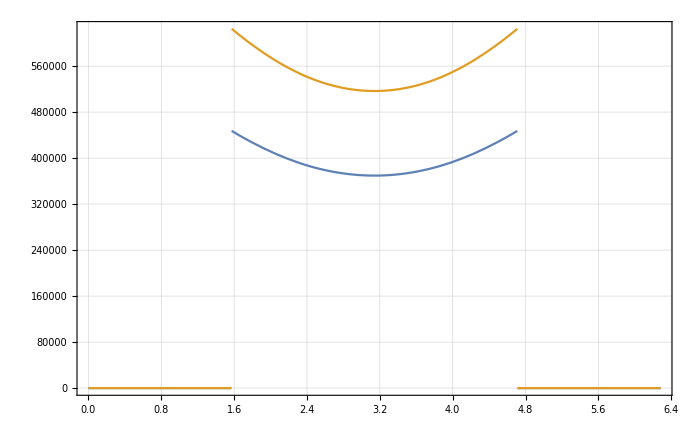

```mathematica
Plot[{pminNBeamCases[phiA,0.,0.03,Pi/4,Pi,0.2,1,1,1,3Pi/2,1,1,1,0.,0.01],pmaxNBeamCases[phiA,0.,0.03,Pi/4,Pi,0.2,1,1,1,3Pi/2,1,1,1,0.,0.01]},{phiA,0,2Pi}]
```

```mathematica
Manipulate[Plot[{pminNBeamCases[phiA,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],pmaxNBeamCases[phiA,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01]},{phiA,0,2Pi}],{phiDet,0,2Pi,2Pi/8}]
```

```mathematica
Manipulate[Plot3D[{pminNBeamCases[phiA,0.,0.03,th0,Pi,0.2,1,1,1,phiA,1,1,1,0.,0.01],pmaxNBeamCases[phiA,0.,0.03,th0,Pi,0.2,1,1,1,phiA,1,1,1,0.,0.01]},{th0,0,Pi/4},{phiA,0,2Pi},PlotRange->All]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

```mathematica
Plot3D[pminNBeamCases[phiA,0.,0.03,Pi/8,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],{phiDet,0,2Pi},{phiA,0,2Pi},PlotRange->All]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

```mathematica
Plot3D[pmaxNBeamCases[phiA,0.,0.03,Pi/8,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],{phiDet,0,2Pi},{phiA,0,2Pi},PlotRange->All]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

```mathematica
Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDV,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{phiDV,0,2*Pi},
{p,pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]}
,PlotPoints->200]
```

-Graphics3D-

```mathematica
Show[
Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDV,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{phiDV,0,2*Pi},
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)420000,680000}
,PlotPoints->100],
ParametricPlot3D[{phiDV,pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],0.0002},{phiDV,0,2Pi},PlotStyle->Red],
ParametricPlot3D[{phiDV,pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],0.0002},{phiDV,0,2Pi},PlotStyle->Red]
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

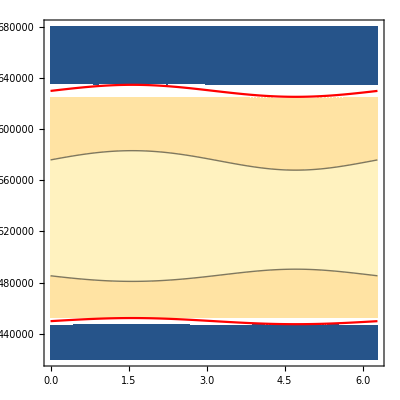

```mathematica
Show[
ContourPlot[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDV,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{phiDV,0,2*Pi},
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)420000,680000}
,PlotPoints->100],
ParametricPlot[{phiDV,pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]},{phiDV,0,2Pi},PlotStyle->Red],
ParametricPlot[{phiDV,pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]},{phiDV,0,2Pi},PlotStyle->Red]
]
```

```mathematica
?pminNBeamCases
```

Global`pminNBeamCases

pminNBeamCases[phiA_,yD_,xD_,th0_?NumericQ,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_?NumericQ,R_,G1_,G2_,xOff_,xAA_]:=Module[{pminlocal=Re[pminNBeam[phiA,yD,xD,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,xOff,xAA]]},Piecewise[{{0,pminlocal<0},{pmax,pminlocal>pmax}},pminlocal]]

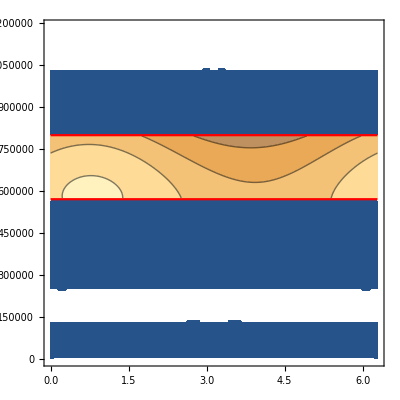

```mathematica
Show[
ContourPlot[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,Pi/2,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{phiDV,0,2*Pi},
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)0,pmax}
,PlotPoints->100],
ParametricPlot[{phiDV,pminNBeamCases[Pi/2,0.,0.03,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.,0.01]},{phiDV,0,2Pi},PlotStyle->Red],
ParametricPlot[{phiDV,pmaxNBeamCases[Pi/2,0.,0.03,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.,0.01]},{phiDV,0,2Pi},PlotStyle->Red]
]
```

```mathematica
Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{Pi/2,phiA,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{phiA,0,2*Pi},
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)0,pmax}
,PlotPoints->100]
```

-Graphics3D-

```mathematica
Integrand2DwNBeamv31[0,0.,0.03,{Pi/2,Pi,Pi,700000,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}]
```

0.

```mathematica
Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{Pi/2,phiA,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{phiA,0,2*Pi},
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)0,pmax}
,PlotPoints->200]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[
Table[{p,phiA,
Re[Integrand2DwNBeamv31[0,0.,0.03,{Pi/2,phiA,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}]]},
{phiA,0,2*Pi,2*Pi/30},
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)0,pmax,pmax/30}],1]
]
```

-Graphics3D-

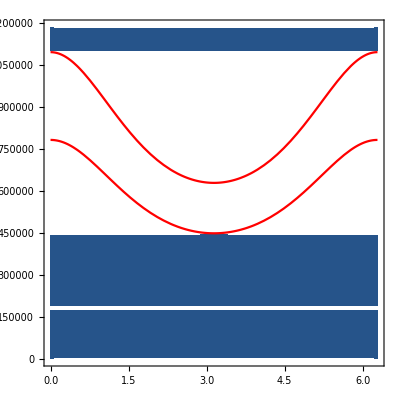

```mathematica
Show[
ContourPlot[
Integrand2DwNBeamv31[0,0.,0.03,{Pi/2,phiA,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{phiA,0,2*Pi},
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)0,pmax}
,PlotPoints->100],
ParametricPlot[{phiA,pminNBeamCases[phiA,0.,0.03,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.,0.01]},{phiA,0,2Pi},PlotStyle->Red],
ParametricPlot[{phiA,pmaxNBeamCases[phiA,0.,0.03,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.,0.01]},{phiA,0,2Pi},PlotStyle->Red]
]
```

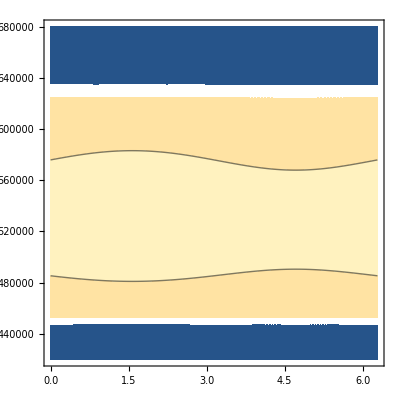

```mathematica
ContourPlot[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDV,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{phiDV,0,2*Pi},
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)420000,680000}
,PlotPoints->100]
```

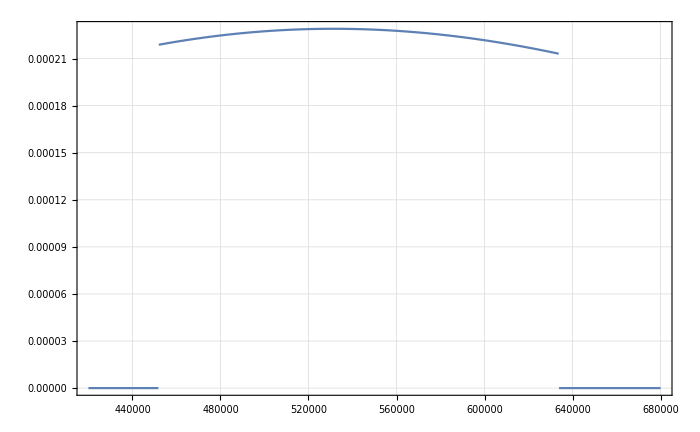

```mathematica
Plot[Integrand2DwNBeamv31[0,0.,0.03,{1,1,1,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)420000,680000}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

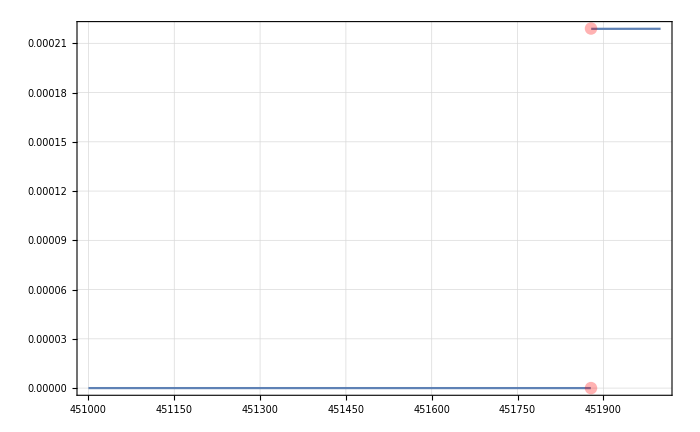

```mathematica
Show[
Plot[Integrand2DwNBeamv31[0,0.,0.03,{1,1,1,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)451000,452000}],
ListPlot[{{pminNBeamCases[1,0.,0.03,Pi/4,Pi,0.2,1,1,1,1,1,1,1,0.,0.01],0},{pminNBeamCases[1,0.,0.03,Pi/4,Pi,0.2,1,1,1,1,1,1,1,0.,0.01],0.000219}},PlotStyle->Directive[Red,Opacity[0.3]]]
]
```

```mathematica
?pminNBeamCases
```

Global`pminNBeamCases

pminNBeamCases[phiA_,yD_,xD_,th0_?NumericQ,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_?NumericQ,R_,G1_,G2_,xOff_,xAA_]:=Module[{pminlocal=Re[pminNBeam[phiA,yD,xD,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2,xOff,xAA]]},Piecewise[{{0,pminlocal<0},{pmax,pminlocal>pmax}},pminlocal]]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

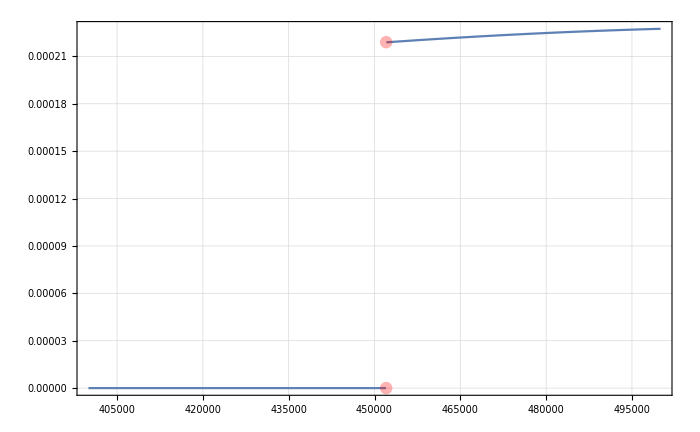

```mathematica
Show[
Plot[Integrand2DwNBeamv31[0,0.,0.03,{2,2,2,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)400000,500000}],
ListPlot[{{pminNBeamCases[2,0.,0.03,Pi/4,Pi,0.2,1,1,1,2,1,1,1,0.,0.01],0},{pminNBeamCases[2,0.,0.03,Pi/4,Pi,0.2,1,1,1,2,1,1,1,0.,0.01],0.000219}},PlotStyle->Directive[Red,Opacity[0.3]]]
]
```

pmin pmax from Nbeam limits

```mathematica
ClearAll[pminNbeam,pmaxNbeam]
```

```mathematica
pminNbeam[phiDV_,yD_,xD_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_,R_,G1_,G2_,twx_,xOff_]:=Solve[DeltaxDV2[phiDV,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]-xOff==twx/2,p][[1,1,2]]
```

```mathematica
pminNbeam[phiDV,0.,0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.06,-0.03]
```

-0.01/(-4.37812×10^-8+1.17933×10^-8 Cos[phiDV])

```mathematica
Plot3D[pminNbeam[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDV,0,2Pi},{phiDet,0,2Pi},PlotRange->{-pmax,pmax},AxesLabel->{"phiDV","phiDet","pmin"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

-Graphics3D-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

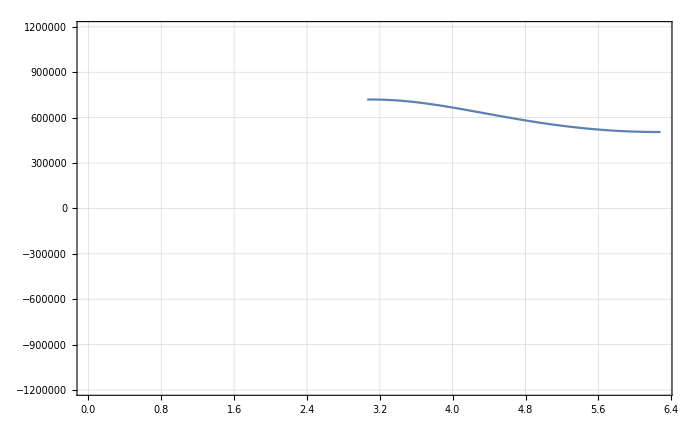

```mathematica
Plot[pminNbeam[Pi,0.,0.04,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDet,0,2Pi},PlotRange->{{0,2Pi},{-pmax,pmax}}]
```

```mathematica
Plot3D[pminNbeam[phiDV,0.,0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDV,0,2Pi},{phiDet,0,2Pi},PlotRange->{-pmax,pmax},AxesLabel->{"phiDV","phiDet","pmin"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

-Graphics3D-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

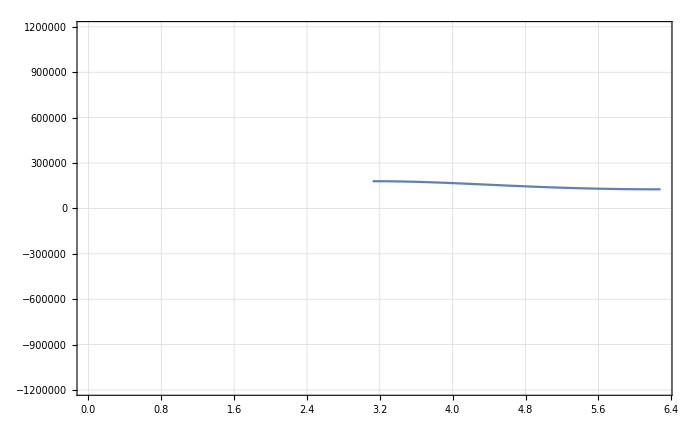

```mathematica
Plot[pminNbeam[Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDet,0,2Pi},PlotRange->{{0,2Pi},{-pmax,pmax}}]
```

```mathematica
Plot3D[pminNbeam[phiDV,0.,-0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDV,0,2Pi},{phiDet,0,2Pi},PlotRange->{-pmax,pmax},AxesLabel->{"phiDV","phiDet","pmin"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

-Graphics3D-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

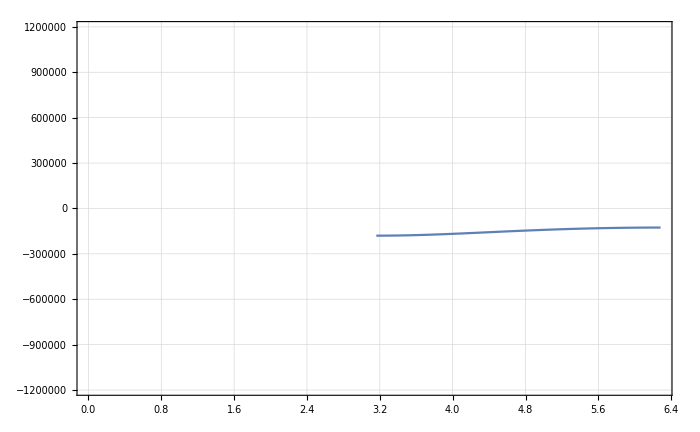

```mathematica
Plot[pminNbeam[Pi,0.,-0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDet,0,2Pi},PlotRange->{{0,2Pi},{-pmax,pmax}}]
```

```mathematica
pmaxNbeam[phiDV_,yD_,xD_,th0_,alpha_,BRxB_,rRxB_,rA_,rD_,phiDet_,R_,G1_,G2_,twx_,xOff_]:=Solve[DeltaxDV2[phiDV,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]-xOff==-twx/2,p][[1,1,2]]
```

```mathematica
pmaxNbeam[Pi/2,0.,-0.03,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.1,-0.03]
```

1.14204×10^6

```mathematica
Plot3D[pmaxNbeam[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDV,0,2Pi},{phiDet,0,2Pi},PlotRange->{-pmax,pmax},AxesLabel->{"phiDV","phiDet","pmax"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

-Graphics3D-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

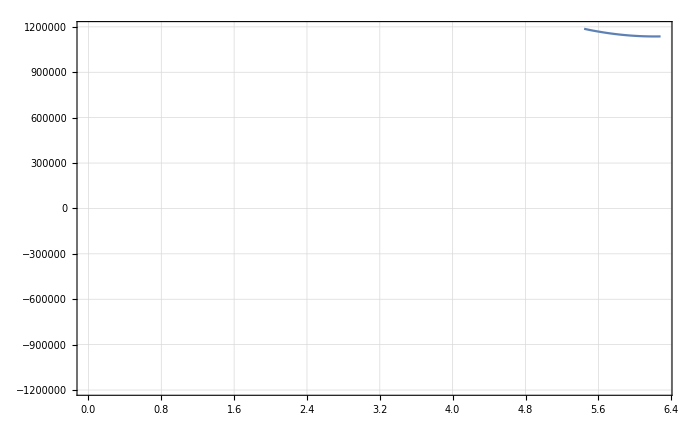

```mathematica
Plot[pmaxNbeam[Pi,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDet,0,2Pi},PlotRange->{{0,2Pi},{-pmax,pmax}}]
```

```mathematica
Plot3D[pmaxNbeam[phiDV,0.,0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDV,0,2Pi},{phiDet,0,2Pi},PlotRange->{-pmax,pmax},AxesLabel->{"phiDV","phiDet","pmax"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

-Graphics3D-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

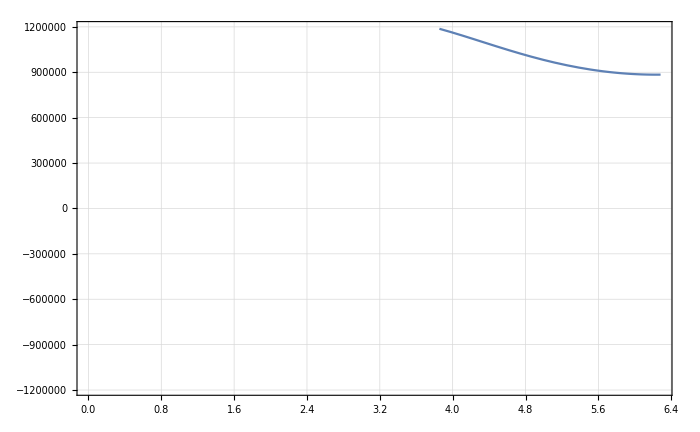

```mathematica
Plot[pmaxNbeam[Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDet,0,2Pi},PlotRange->{{0,2Pi},{-pmax,pmax}}]
```

```mathematica
Plot3D[pmaxNbeam[phiDV,0.,-0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDV,0,2Pi},{phiDet,0,2Pi},PlotRange->{-pmax,pmax},AxesLabel->{"phiDV","phiDet","pmax"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

-Graphics3D-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

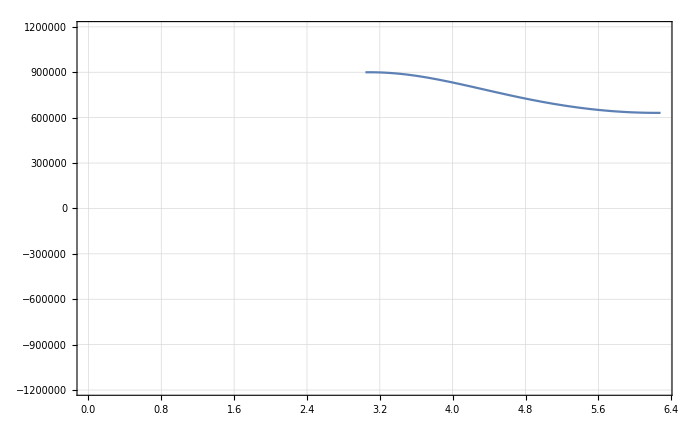

```mathematica
Plot[pmaxNbeam[Pi,0.,-0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDet,0,2Pi},PlotRange->{{0,2Pi},{-pmax,pmax}}]
```

```mathematica
pmaxNbeam[0,0.,-0.01,Pi/4,Pi,0.2,1,1,1,2Pi,1,1,1,0.06,-0.03]
```

899693.

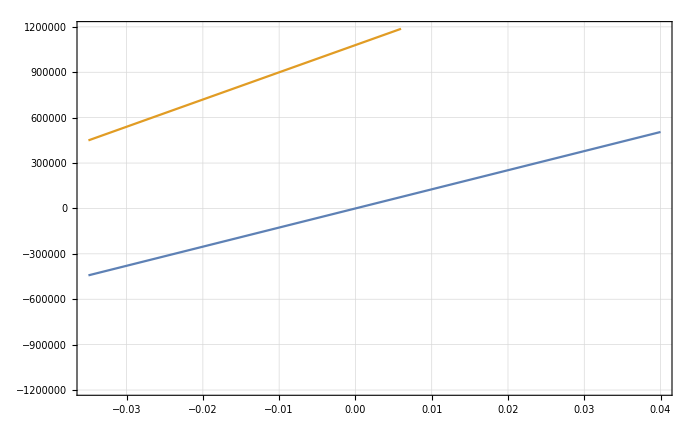

```mathematica
Plot[{pminNbeam[Pi,0.,xD,Pi/4,Pi,0.2,1,1,1,2Pi,1,1,1,0.06,-0.03],pmaxNbeam[0,0.,xD,Pi/4,Pi,0.2,1,1,1,2Pi,1,1,1,0.06,-0.03]},{xD,-0.035,0.04},PlotRange->{Automatic,{-pmax,pmax}}]
```

```mathematica
?Integrand2DwNBeamv31
```

Global`Integrand2DwNBeamv31

Integrand2DwNBeamv31[b_,yD_,xD_,{phiDV_?NumericQ,phiA_?NumericQ,phiDet_?NumericQ,p_?NumericQ,th0_?NumericQ},{alpha_,BRxB_,rRxB_,rA_,rD_,R_,G1_,G2_},{twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_},{xAA_,yAA_,xOff_,yOff_}]:=wmomNormedWb[λ0,κ0,b,p] Sin[th0] TrapezNBeamNewNormed[DeltaxDV2[phiDV,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2]-xOff,{twx,plx,k1x,k2x,k3x}] TrapezNBeamNewNormed[DeltayDV[phiDV,yD,p,th0,BRxB,rRxB,rA,rD,phiDet]-yOff,{twy,ply,k1y,k2y,k3y}] ApertBoole[xA[phiA,yD,xD,p,th0,alpha,BRxB,rRxB,rA,rD,phiDet,R,G1,G2],yA[phiA,yD,p,th0,BRxB,rRxB,rA,rD,phiDet],{xAA,yAA,xOff,yOff}]

```mathematica
Show[
Plot3D[
Integrand2DwNBeamv31[0,0.,0.01,{phiDV,phiDV+Pi,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},
{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},
{0.01,0.035,-0.03,0.}],
{phiDV,0,2*Pi},{p,0,pmax},PlotPoints->50,PlotRange->{Automatic,{0,pmax},Automatic}],

ParametricPlot3D[{
{phiDV,pminNbeam[phiDV+Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,2Pi,1,1,1,0.06,-0.03],0.00001},
{phiDV,pmaxNbeam[phiDV+Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,2Pi,1,1,1,0.06,-0.03],0.00001}
},{phiDV,0,2Pi},PlotStyle->{Red,Darker[Red]}](*,

ParametricPlot3D[{
{phiDV,pminApert[Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],0.0001},
{phiDV,pmaxApert[Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],0.0001}
},{phiDV,0,2Pi},PlotStyle->{Purple,Darker[Purple]}]*)
]
```

-Graphics3D-

### WHAT THE HELL, if I give Phi shift to phiDV, I get the correct shape for better pmax limit. in pmin, it doesnt help much!. Check with different Integrand parameters

```mathematica
Show[
Plot3D[
Integrand2DwNBeamv31[0,0.,-0.01,{phiDV,2Pi,2Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},
{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},
{0.01,0.035,-0.03,0.}],
{phiDV,0,2*Pi},{p,0,pmax},PlotPoints->50,PlotRange->{Automatic,{0,pmax},Automatic}],

ParametricPlot3D[{
{phiDV,pminNbeam[phiDV+Pi,0.,-0.01,Pi/4,Pi,0.2,1,1,1,2Pi,1,1,1,0.06,-0.03],0.00001},
{phiDV,pmaxNbeam[phiDV+Pi,0.,-0.01,Pi/4,Pi,0.2,1,1,1,2Pi,1,1,1,0.06,-0.03],0.00001}
},{phiDV,0,2Pi},PlotStyle->{Red,Darker[Red]}](*,

ParametricPlot3D[{
{phiDV,pminApert[Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],0.0001},
{phiDV,pmaxApert[Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],0.0001}
},{phiDV,0,2Pi},PlotStyle->{Purple,Darker[Purple]}]*)
]
```

-Graphics3D-

### only if I correlate phiA with phiDV, do I get a oscillating integrand in the 3D plot. if phiA fixed, no oscillation!

```mathematica
Show[
Plot3D[
Integrand2DwNBeamv31[0,0.,0.01,{phiDV,phiDV,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.}],{phiDV,0,2*Pi},{p,0,pmax},PlotPoints->50,PlotRange->{Automatic,{0,pmax},Automatic}],

ParametricPlot3D[{
{phiDV,pminNbeam[phiDV,0.,0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.06,-0.03],0.0001},
{phiDV,pmaxNbeam[phiDV,0.,0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.06,-0.03],0.0001}
},{phiDV,0,2Pi},PlotStyle->{Red,Darker[Red]}],

ParametricPlot3D[{
{phiDV,pminApert[Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],0.0001},
{phiDV,pmaxApert[Pi,0.,0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],0.0001}
},{phiDV,0,2Pi},PlotStyle->{Purple,Darker[Purple]}]
]
```

-Graphics3D-

```mathematica
Show[
Plot3D[
Integrand2DwNBeamv31[0,0.,-0.01,{phiDV,phiDV+Pi/2,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.}],{phiDV,0,2*Pi},{p,0,pmax},PlotPoints->50,PlotRange->{Automatic,{0,pmax},Automatic}],
ParametricPlot3D[{
{phiDV,pminNbeam[phiDV,0.,-0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.06,-0.03],0.0001},
{phiDV,pmaxNbeam[phiDV,0.,-0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.06,-0.03],0.0001}
},{phiDV,0,2Pi},PlotStyle->{Red,Darker[Red]}],
ParametricPlot3D[{
{phiDV,pminApert[Pi,0.,-0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],0.0001},
{phiDV,pmaxApert[Pi,0.,-0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],0.0001}
},{phiDV,0,2Pi},PlotStyle->{Purple,Darker[Purple]}]
]
```

-Graphics3D-

```mathematica
Pitch[p_,th_,B_]:=2*Pi*p*Cos[th]/c/B
```

```mathematica
Pitch[pmax,Pi/4,0.2]
```

0.0879769

```mathematica
Plot3D[Pitch[p,th,0.2],{p,0,pmax},{th,0,Pi/4}]
```

-Graphics3D-

```mathematica
ApertToDet[yatA_,R_,zA_,zDet_]:=(yatA+R)*Pi+zA+zDet
```

```mathematica
ApertToDet[0,1,0.3,0.4]
```

3.84159

```mathematica
ApertToDet[0,1,0.3,0.4]/Pitch[pmax,Pi/4,0.2]
```

43.6659

```mathematica
Mod[ApertToDet[0,1,0.3,0.4]/Pitch[0.1,Pi/8,0.2],1]
```

0.239338

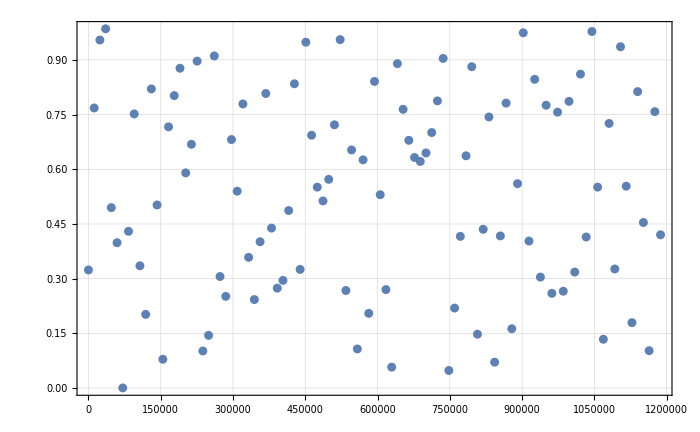

```mathematica
ListPlot[Table[{p,Mod[ApertToDet[0,1,0.3,0.4]/Pitch[p,Pi/8,0.2],1]},{p,1,pmax,(pmax-1)/100}]]
```

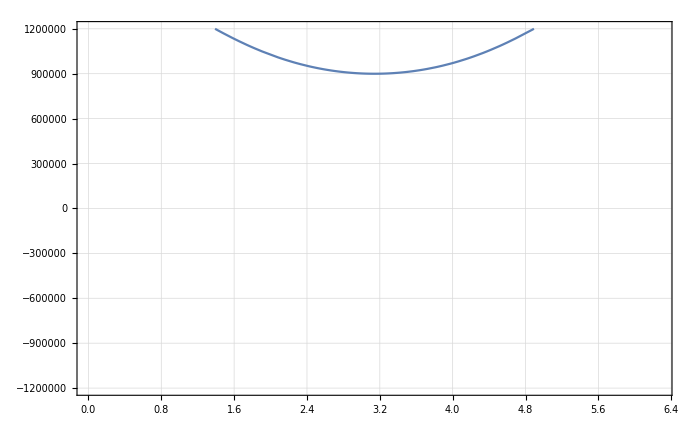

```mathematica
Plot[pminNbeam[phiDV,0.,-0.01,Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,0.06,-0.03],{phiDV,0,2Pi},PlotRange->{-1.2*10^6,1.2*10^6},PlotPoints->10]
```

```mathematica
Plot3D[pminNbeam[phiDV,0.,xD,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.06,-0.03],{phiDV,0,2Pi},{xD,-0.06,0.06},PlotRange->{-1.2*10^6,1.2*10^6},PlotPoints->10]
```

```mathematica
Plot3D[pminNbeam[phiDV,0.,0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDV,0,2Pi},{phiDet,0,2Pi},PlotRange->{-1.2*10^6,1.2*10^6},PlotPoints->10]
```

-Graphics3D-

```mathematica
Plot3D[pminNbeam[phiDV,0.,-0.01,Pi/4,Pi,0.2,1,1,1,phiDet,1,1,1,0.06,-0.03],{phiDV,0,2Pi},{phiDet,0,2Pi},PlotRange->{-1.2*10^6,1.2*10^6},PlotPoints->10]
```

-Graphics3D-

```mathematica
Show[
Plot3D[
Integrand2DwNBeamv31[
0,0.,-0.01,{phiDV,phiDV+Pi/2,3*Pi/2,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},
{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},
{0.01,0.035,-0.03,0.}],
{phiDV,0,2*Pi},{p,0,pmax},PlotPoints->50],
ParametricPlot3D[{
{phiDV,pminNbeam[phiDV,0.,-0.01,Pi/4,Pi,0.2,1,1,1,3*Pi/2,1,1,1,0.06,-0.03],0.0001},
{phiDV,pmaxNbeam[phiDV,0.,-0.01,Pi/4,Pi,0.2,1,1,1,3*Pi/2,1,1,1,0.06,-0.03],0.0001}
},{phiDV,0,2Pi}]
]
```

-Graphics3D-

First integration test

```mathematica
testTable=ParallelTable[{
xD,
yD,
NIntegrate[
Integrand2DwNBeamv31[0.,phiDV,phiDV,yD,xD,p,th0,Pi,0.2,1.,1.,1.,phiDV,1.,1.,1.,{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],{th0,0,Pi/4},{phiDV,0,2*Pi},
{p,pminNBeamCases[phiDV,phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->False}]},{xD,-0.005,0.07,0.005},{yD,-0.045,0.045,0.01}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{{-0.005,-0.045,0.},{-0.005,-0.035,0.},{-0.005,-0.025,0.},{-0.005,-0.015,0.},{-0.005,-0.005,0.},{-0.005,0.005,0.},{-0.005,0.015,0.},{-0.005,0.025,0.},{-0.005,0.035,0.},{-0.005,0.045,0.}},{{0.,-0.045,0.},{0.,-0.035,0.},{0.,-0.025,0.},{0.,-0.015,0.880255},{0.,-0.005,1.10026},{0.,0.005,1.3077},{0.,0.015,1.50333},{0.,0.025,0.},{0.,0.035,0.},{0.,0.045,0.}},{{0.005,-0.045,0.},{0.005,-0.035,0.},{0.005,-0.025,0.},{0.005,-0.015,6.37679},{0.005,-0.005,7.96956},{0.005,0.005,9.47081},{0.005,0.015,10.8858},{0.005,0.025,0.},{0.005,0.035,0.},{0.005,0.045,0.}},{{0.01,-0.045,0.},{0.01,-0.035,0.},{0.01,-0.025,0.},{0.01,-0.015,19.0956},{0.01,-0.005,23.8879},{0.01,0.005,28.4135},{0.01,0.015,32.6872},{0.01,0.025,0.},{0.01,0.035,0.},{0.01,0.045,0.}},{{0.015,-0.045,0.},{0.015,-0.035,0.},{0.015,-0.025,0.},{0.015,-0.015,36.7162},{0.015,-0.005,46.0178},{0.015,0.005,54.8368},{0.015,0.015,63.1972},{0.015,0.025,0.},{0.015,0.035,0.},{0.015,0.045,0.}},{{0.02,-0.045,0.},{0.02,-0.035,0.},{0.02,-0.025,0.},{0.02,-0.015,55.2055},{0.02,-0.005,69.3863},{0.02,0.005,82.9099},{0.02,0.015,95.8036},{0.02,0.025,0.},{0.02,0.035,0.},{0.02,0.045,0.}},{{0.025,-0.045,0.},{0.025,-0.035,0.},{0.025,-0.025,0.},{0.025,-0.015,70.5498},{0.025,-0.005,89.0123},{0.025,0.005,106.756},{0.025,0.015,123.801},{0.025,0.025,0.},{0.025,0.035,0.},{0.025,0.045,0.}},{{0.03,-0.045,0.},{0.03,-0.035,0.},{0.03,-0.025,0.},{0.03,-0.015,79.5382},{0.03,-0.005,100.868},{0.03,0.005,121.573},{0.03,0.015,141.657},{0.03,0.025,0.},{0.03,0.035,0.},{0.03,0.045,0.}},{{0.035,-0.045,0.},{0.035,-0.035,0.},{0.035,-0.025,0.},{0.035,-0.015,80.2426},{0.035,-0.005,102.473},{0.035,0.005,124.337},{0.035,0.015,145.812},{0.035,0.025,0.},{0.035,0.035,0.},{0.035,0.045,0.}},{{0.04,-0.045,0.},{0.04,-0.035,0.},{0.04,-0.025,0.},{0.04,-0.015,72.2735},{0.04,-0.005,93.2162},{0.04,0.005,114.18},{0.04,0.015,135.113},{0.04,0.025,0.},{0.04,0.035,0.},{0.04,0.045,0.}},{{0.045,-0.045,0.},{0.045,-0.035,0.},{0.045,-0.025,0.},{0.045,-0.015,56.9045},{0.045,-0.005,74.5133},{0.045,0.005,92.5833},{0.045,0.015,111.044},{0.045,0.025,0.},{0.045,0.035,0.},{0.045,0.045,0.}},{{0.05,-0.045,0.},{0.05,-0.035,0.},{0.05,-0.025,0.},{0.05,-0.015,37.1288},{0.05,-0.005,49.8776},{0.05,0.005,63.4633},{0.05,0.015,77.8185},{0.05,0.025,0.},{0.05,0.035,0.},{0.05,0.045,0.}},{{0.055,-0.045,0.},{0.055,-0.035,0.},{0.055,-0.025,0.},{0.055,-0.015,17.6777},{0.055,-0.005,24.9472},{0.055,0.005,33.2052},{0.055,0.015,42.4291},{0.055,0.025,0.},{0.055,0.035,0.},{0.055,0.045,0.}},{{0.06,-0.045,0.},{0.06,-0.035,0.},{0.06,-0.025,0.},{0.06,-0.015,4.65771},{0.06,-0.005,7.23353},{0.06,0.005,10.5271},{0.06,0.015,14.5869},{0.06,0.025,0.},{0.06,0.035,0.},{0.06,0.045,0.}},{{0.065,-0.045,0.},{0.065,-0.035,0.},{0.065,-0.025,0.},{0.065,-0.015,0.289638},{0.065,-0.005,0.604699},{0.065,0.005,1.12825},{0.065,0.015,1.92978},{0.065,0.025,0.},{0.065,0.035,0.},{0.065,0.045,0.}},{{0.07,-0.045,0.},{0.07,-0.035,0.},{0.07,-0.025,0.},{0.07,-0.015,0.},{0.07,-0.005,0.000608414},{0.07,0.005,0.00363481},{0.07,0.015,0.0141364},{0.07,0.025,0.},{0.07,0.035,0.},{0.07,0.045,0.}}}

```mathematica
ListPlot3D[Flatten[%,1]]
```

-Graphics3D-

### here the issue is there, that we set alle phase angles the same -> a angle that barely goes through aperture is the exact same as at det, so only close to edge of aperture! therefore very sharp edges of transported spectrum

```mathematica
Manipulate[Show[
Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDet,p,th0},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,0.,0.}],
{phiDV,0,2*Pi},
{p,(*pminNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],pmaxNBeamCases[phiDV,0.,0.03,Pi/4,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01]*)0,pmax}
,PlotPoints->10],
ParametricPlot3D[{phiDV,pminNBeamCases[phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],0.00002},{phiDV,0,2Pi},PlotStyle->Red],
ParametricPlot3D[{phiDV,pmaxNBeamCases[phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDV,1,1,1,0.,0.01],0.00002},{phiDV,0,2Pi},PlotStyle->Red]
],{th0,0,Pi/4},{phiDet,0,2*Pi}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Manipulate[Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDet,p,th0},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}],
{phiDV,0,2*Pi},
{
p,
pminNBeamCases[phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],
pmaxNBeamCases[phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01]
},PlotRange->All,PlotPoints->15],{th0,0,Pi/4},{phiDet,0,2*Pi}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Plot3D::nlnum: The function value {pminNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01],pmaxNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01]} is not a list of numbers with dimensions {2} at {phiDV} = {0.}.

Visualization`Core`Plot3D::invfuncs: -- Message text not found -- (Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,FE`phiDet$$487,p,FE`th0$$487},{π,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}])

Plot3D::nlnum: The function value {pminNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01],pmaxNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01]} is not a list of numbers with dimensions {2} at {phiDV} = {0.}.

Visualization`Core`Plot3D::invfuncs: -- Message text not found -- (Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,FE`phiDet$$487,p,FE`th0$$487},{π,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}])

Plot3D::nlnum: The function value {pminNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01],pmaxNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01]} is not a list of numbers with dimensions {2} at {phiDV} = {0.}.

General::stop: Further output of Plot3D::nlnum will be suppressed during this calculation.

Visualization`Core`Plot3D::invfuncs: -- Message text not found -- (Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,FE`phiDet$$487,p,FE`th0$$487},{π,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}])

General::stop: Further output of Visualization`Core`Plot3D::invfuncs will be suppressed during this calculation.

Plot3D::nlnum: The function value {pminNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01],pmaxNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01]} is not a list of numbers with dimensions {2} at {phiDV} = {0.}.

Visualization`Core`Plot3D::invfuncs: -- Message text not found -- (Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,FE`phiDet$$487,p,FE`th0$$487},{π,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}])

Plot3D::nlnum: The function value {pminNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01],pmaxNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01]} is not a list of numbers with dimensions {2} at {phiDV} = {0.}.

Visualization`Core`Plot3D::invfuncs: -- Message text not found -- (Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,FE`phiDet$$487,p,FE`th0$$487},{π,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}])

Plot3D::nlnum: The function value {pminNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01],pmaxNBeamCases[0.,0.,0.03,0.43354,3.14159,0.2,1.,1.,1.,3.54372,1.,1.,1.,0.,0.01]} is not a list of numbers with dimensions {2} at {phiDV} = {0.}.

General::stop: Further output of Plot3D::nlnum will be suppressed during this calculation.

Visualization`Core`Plot3D::invfuncs: -- Message text not found -- (Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,FE`phiDet$$487,p,FE`th0$$487},{π,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}])

General::stop: Further output of Visualization`Core`Plot3D::invfuncs will be suppressed during this calculation.

```mathematica
Manipulate[Plot3D[
Integrand2DwNBeamv31[0,0.,0.03,{phiDV,phiDV,phiDet,p,th0},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}],
{phiDV,0,2*Pi},
{
p,
(*pminNBeamCases[phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],
pmaxNBeamCases[phiDV,0.,0.03,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01]*)0,pmax
},PlotRange->All,PlotPoints->15],{th0,0,Pi/4},{phiDet,0,2*Pi}]
```

```mathematica
t0=AbsoluteTime[];
testTable2=ParallelTable[{
xD,
yD,
NIntegrate[
Integrand2DwNBeamv31[0,yD,xD,{phiDV,phiDV,phiDet,p,th0},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}],{th0,0,Pi/4},{phiDet,0,2*Pi},{phiDV,0,2*Pi},
{
p,
(*pminNBeamCases[phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],
pmaxNBeamCases[phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01]*)0,pmax
},
PrecisionGoal->4,Method->"AdaptiveMonteCarlo",AccuracyGoal->6,MaxPoints->300000]
},{xD,-0.005,0.075,0.01},{yD,-0.04,0.04,0.01},Method->"FinestGrained"]
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 61.969 and 0.12002 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 126.076 and 1.06671 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 326.882 and 0.912436 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 129.595 and 0.859414 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 59.8083 and 0.160629 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 543.36 and 2.53773 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 317.775 and 0.681051 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 523.683 and 2.0747 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 57.4442 and 0.22514 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 570.113 and 1.76567 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 311.919 and 1.11855 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 586.8 and 2.51504 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 93.4799 and 0.284845 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 39.4906 and 0.30274 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 334.389 and 1.58061 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 130.907 and 0.461887 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 393.08 and 1.27823 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 6.53931 and 0.0655095 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 159.768 and 0.469742 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 0.0878305 and 0.00131343 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 23.747 and 0.282107 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 3.21045 and 0.01548 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 32.1632 and 0.326965 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 300100 integrand evaluations. NIntegrate obtained 2.36709 and 0.0272913 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{{{-0.005,-0.04,0.},{-0.005,-0.03,0.},{-0.005,-0.02,0.},{-0.005,-0.01,0.},{-0.005,0.,0.},{-0.005,0.01,0.},{-0.005,0.02,0.},{-0.005,0.03,0.},{-0.005,0.04,0.}},{{0.005,-0.04,0.},{0.005,-0.03,0.},{0.005,-0.02,0.},{0.005,-0.01,61.969},{0.005,0.,59.8083},{0.005,0.01,57.4442},{0.005,0.02,0.},{0.005,0.03,0.},{0.005,0.04,0.}},{{0.015,-0.04,0.},{0.015,-0.03,0.},{0.015,-0.02,0.},{0.015,-0.01,326.882},{0.015,0.,317.775},{0.015,0.01,311.919},{0.015,0.02,0.},{0.015,0.03,0.},{0.015,0.04,0.}},{{0.025,-0.04,0.},{0.025,-0.03,0.},{0.025,-0.02,126.076},{0.025,-0.01,543.36},{0.025,0.,570.113},{0.025,0.01,532.405},{0.025,0.02,121.99},{0.025,0.03,0.},{0.025,0.04,0.}},{{0.035,-0.04,0.},{0.035,-0.03,0.},{0.035,-0.02,129.595},{0.035,-0.01,523.683},{0.035,0.,586.8},{0.035,0.01,529.787},{0.035,0.02,138.743},{0.035,0.03,0.},{0.035,0.04,0.}},{{0.045,-0.04,0.},{0.045,-0.03,0.},{0.045,-0.02,93.4799},{0.045,-0.01,334.389},{0.045,0.,393.08},{0.045,0.01,342.034},{0.045,0.02,93.6868},{0.045,0.03,8.70179},{0.045,0.04,0.}},{{0.055,-0.04,0.},{0.055,-0.03,0.},{0.055,-0.02,39.4906},{0.055,-0.01,130.907},{0.055,0.,159.768},{0.055,0.01,141.426},{0.055,0.02,55.5597},{0.055,0.03,9.17963},{0.055,0.04,0.}},{{0.065,-0.04,0.},{0.065,-0.03,0.},{0.065,-0.02,6.53931},{0.065,-0.01,23.747},{0.065,0.,32.1632},{0.065,0.01,30.8569},{0.065,0.02,8.00436},{0.065,0.03,1.83142},{0.065,0.04,0.}},{{0.075,-0.04,0.},{0.075,-0.03,0.},{0.075,-0.02,0.0878305},{0.075,-0.01,3.21045},{0.075,0.,2.36709},{0.075,0.01,0.},{0.075,0.02,0.},{0.075,0.03,0.},{0.075,0.04,0.}}}

798.476302

```mathematica
ListPlot3D[Flatten[testTable2,1],InterpolationOrder->2]
```

-Graphics3D-

```mathematica
testTable3=ParallelTable[{
xD,
yD,
NIntegrate[
Integrand2DwNBeamv31[0,yD,xD,{phiDV,phiDV,phiDet,p,th0},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}],{th0,0,Pi/4},{phiDet,0,2*Pi},{phiDV,0,2*Pi},
{
p,
pminNBeamCases[phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],
pmaxNBeamCases[phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01]
},
PrecisionGoal->4,Method->"AdaptiveMonteCarlo",AccuracyGoal->6,MaxPoints->300000]
},{xD,-0.005,0.075,0.01},{yD,-0.04,0.04,0.01},Method->"FinestGrained"]
```

{{{-0.005,-0.04,0.},{-0.005,-0.03,0.},{-0.005,-0.02,0.},{-0.005,-0.01,0.},{-0.005,0.,0.},{-0.005,0.01,0.},{-0.005,0.02,0.},{-0.005,0.03,0.},{-0.005,0.04,0.}},{{0.005,-0.04,0.},{0.005,-0.03,0.},{0.005,-0.02,0.},{0.005,-0.01,0.},{0.005,0.,0.},{0.005,0.01,0.},{0.005,0.02,0.},{0.005,0.03,0.},{0.005,0.04,0.}},{{0.015,-0.04,0.},{0.015,-0.03,0.},{0.015,-0.02,0.},{0.015,-0.01,0.},{0.015,0.,0.},{0.015,0.01,0.},{0.015,0.02,0.},{0.015,0.03,0.},{0.015,0.04,0.}},{{0.025,-0.04,0.},{0.025,-0.03,0.},{0.025,-0.02,0.},{0.025,-0.01,0.},{0.025,0.,0.},{0.025,0.01,0.},{0.025,0.02,0.},{0.025,0.03,0.},{0.025,0.04,0.}},{{0.035,-0.04,0.},{0.035,-0.03,0.},{0.035,-0.02,0.},{0.035,-0.01,0.},{0.035,0.,0.},{0.035,0.01,0.},{0.035,0.02,0.},{0.035,0.03,0.},{0.035,0.04,0.}},{{0.045,-0.04,0.},{0.045,-0.03,0.},{0.045,-0.02,0.},{0.045,-0.01,0.},{0.045,0.,0.},{0.045,0.01,0.},{0.045,0.02,0.},{0.045,0.03,0.},{0.045,0.04,0.}},{{0.055,-0.04,0.},{0.055,-0.03,0.},{0.055,-0.02,0.},{0.055,-0.01,0.},{0.055,0.,0.},{0.055,0.01,0.},{0.055,0.02,0.},{0.055,0.03,0.},{0.055,0.04,0.}},{{0.065,-0.04,0.},{0.065,-0.03,0.},{0.065,-0.02,0.},{0.065,-0.01,0.},{0.065,0.,0.},{0.065,0.01,0.},{0.065,0.02,0.},{0.065,0.03,0.},{0.065,0.04,0.}},{{0.075,-0.04,0.},{0.075,-0.03,0.},{0.075,-0.02,0.},{0.075,-0.01,0.},{0.075,0.,0.},{0.075,0.01,0.},{0.075,0.02,0.},{0.075,0.03,0.},{0.075,0.04,0.}}}

```mathematica
ListPlot3D[Flatten[testTable3,1]]
```

-Graphics3D-

```mathematica
Integrand2DwNBeamv31[0,0.,0.,{0.,0.,0.,0.,0.},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.}]
```

0.

```mathematica
t0=AbsoluteTime[];
testTable4=ParallelTable[{
xD,
yD,
NIntegrate[
Integrand2DwNBeamv31[0,yD,xD,{phiDV,phiA,phiDet,p,th0},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}],{th0,0,Pi/4},{phiDet,0,2*Pi},{phiA,0,2Pi},{phiDV,0,2*Pi},
{
p,
(*pminNBeamCases[phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],
pmaxNBeamCases[phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01]*)0,pmax
},
PrecisionGoal->3,Method->"AdaptiveMonteCarlo",AccuracyGoal->5,MaxPoints->500000]
},{xD,-0.005,0.075,0.01},{yD,-0.03,0.03,0.01},Method->"FinestGrained"]
t1=AbsoluteTime[];
t1-t0
```

$Aborted

20.22887

```mathematica
ListPlot3D[Flatten[testTable2,1]]
```

-Graphics3D-

```mathematica
ListPlot3D[Flatten[testTable4,1]]
```

-Graphics3D-

```mathematica
ListPlot3D[
Transpose[{
Flatten[testTable2,1][[All,1]],Flatten[testTable2,1][[All,2]],
Flatten[testTable2,1][[All,3]]/Total[Flatten[testTable2,1][[All,3]]]-Flatten[testTable4,1][[All,3]]/Total[Flatten[testTable4,1][[All,3]]]
}]
,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[
Transpose[{
Flatten[testTable2,1][[All,1]],Flatten[testTable2,1][[All,2]],
(Flatten[testTable2,1][[All,3]]/Total[Flatten[testTable2,1][[All,3]]]-Flatten[testTable4,1][[All,3]]/Total[Flatten[testTable4,1][[All,3]]])/Flatten[testTable2,1][[All,3]]/Total[Flatten[testTable2,1][[All,3]]]
}]
,PlotRange->All]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics3D-

```mathematica
t0=AbsoluteTime[];
testTable5=ParallelTable[{
xD,
yD,
NIntegrate[
Integrand2DwNBeamv31[0,yD,xD,{phiDV,phiA,phiDet,p,th0},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.}],{th0,0,Pi/4},{phiDet,0,2*Pi},{phiA,0,2Pi},{phiDV,0,2*Pi},
{
p,
(*pminNBeamCases[phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01],
pmaxNBeamCases[phiDV,yD,xD,th0,Pi,0.2,1,1,1,phiDet,1,1,1,0.,0.01]*)0,pmax
},
PrecisionGoal->4,Method->"GlobalAdaptive",AccuracyGoal->6]
},{xD,-0.005,0.075,0.01},{yD,-0.04,0.04,0.01},Method->"FinestGrained"]
t1=AbsoluteTime[];
t1-t0
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 114.108 and 114.108 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1070.31 and 200.545 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2102.38 and 41.2767 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 843.05 and 55.1103 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

233.9794

Fits

```mathematica
Get["TransportFunctions/XDataCreation.m"];
```

```mathematica
XYDatam05p75=XYDataCreation[{-0.005,0.075,-0.04,7},{-0.03,0.03,0.,5}]
```

{{-0.045,-0.03},{-0.045,-0.015},{-0.045,0.},{-0.045,0.015},{-0.045,0.03},{-0.0316667,-0.03},{-0.0316667,-0.015},{-0.0316667,0.},{-0.0316667,0.015},{-0.0316667,0.03},{-0.0183333,-0.03},{-0.0183333,-0.015},{-0.0183333,0.},{-0.0183333,0.015},{-0.0183333,0.03},{-0.005,-0.03},{-0.005,-0.015},{-0.005,0.},{-0.005,0.015},{-0.005,0.03},{0.00833333,-0.03},{0.00833333,-0.015},{0.00833333,0.},{0.00833333,0.015},{0.00833333,0.03},{0.0216667,-0.03},{0.0216667,-0.015},{0.0216667,0.},{0.0216667,0.015},{0.0216667,0.03},{0.035,-0.03},{0.035,-0.015},{0.035,0.},{0.035,0.015},{0.035,0.03}}

### memoization

```mathematica
ClearAll[FitFuncMemoArith]
```

```mathematica
FitFuncTablewNbeam[b_,XYData_List,{alpha_,BRxB_,rF_,rA_,rRxB_,rD_,R_,G1_,G2_},{twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_},{xAA_,yAA_,xOff_,yOff_},IntPrec_]:=
FitFuncTablewNbeam[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]=
Integration2DwNBeamc31[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]
```

```mathematica
Integration2DwNBeamc31[0.,{{0.,0.},{0.03,0.02}},{Pi,0.2,2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},3]
```

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained 10.9617 and 0.0922833 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 500100 integrand evaluations. NIntegrate obtained 3174.15 and 7.10067 for the integral and error estimates.

{{0.,0.,3174.15},{0.03,0.02,10.9617}}

```mathematica
Integration2DwNBeamc31[0.,{{0.03499999999999998,0.015},{0.03499999999999998,0.03}},{Pi,0.2,2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},3]
```

$Aborted

### bin selection and normalization

```mathematica
FitFuncBinwNbeam[bin_?NumericQ,b_?NumericQ,XYData_List,{alpha_?NumericQ,BRxB_?NumericQ,rF_?NumericQ,rA_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,R_?NumericQ,G1_?NumericQ,G2_?NumericQ},{twx_?NumericQ,plx_?NumericQ,k1x_?NumericQ,k2x_?NumericQ,k3x_?NumericQ,twy_?NumericQ,ply_?NumericQ,k1y_?NumericQ,k2y_?NumericQ,k3y_?NumericQ},{xAA_?NumericQ,yAA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ},IntPrec_]:=
FitFuncTablewNbeam[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec][[bin]]/Total[FitFuncTablewNbeam[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]]
```

### testdata

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeam=Table[{bin,FitFuncBinwNbeam[bin,0.,XYDatam05p75,{Pi,0.2,2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75]}]
t1=AbsoluteTime[];
t1-t0
```

Wed 11 Dec 2019 13:53:57

NIntegrate::maxp: The integral failed to converge after 2500100 integrand evaluations. NIntegrate obtained 2459.44 and 3.36853 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 2500100 integrand evaluations. NIntegrate obtained 817.902 and 0.673526 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 2500100 integrand evaluations. NIntegrate obtained 766.611 and 0.646345 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 2500100 integrand evaluations. NIntegrate obtained 712.211 and 0.532882 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 2500100 integrand evaluations. NIntegrate obtained 2564.81 and 4.36904 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 2500100 integrand evaluations. NIntegrate obtained 3172.2 and 2.10974 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 2500100 integrand evaluations. NIntegrate obtained 3727.68 and 4.23368 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 2500100 integrand evaluations. NIntegrate obtained 2338.68 and 3.0983 for the integral and error estimates.

$Aborted

1435.84108

```mathematica
ListPlot3D[Transpose[{XYDatam05p75[[All,1]],XYDatam05p75[[All,2]],ElectronData180wFilter2DwNbeam[[All,2]]}],InterpolationOrder->2]
```

-Graphics3D-

### testfit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
Electron2D180wFilterBRxBFit=Reap[NonlinearModelFit[
ElectronData180wFilter2DwNbeam,
{
FitFuncBinwNbeam[bin,b,XYDatam05p75,{Pi,0.2+0.2*5*10^-5,2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},3],
-0.002<b<0.002
},
{{b,-0.001}},bin,MaxIterations->8,EvaluationMonitor:>Sow[b],Method->"NMinimize",PrecisionGoal->5,AccuracyGoal->6
]
];
t1=AbsoluteTime[];
t1-t0
```

Tue 19 Nov 2019 10:07:13

$Aborted

4.214395